## Numerical Example (Homog. b.c. for u and p):

```mathematica
lambda=0;
mu=1;
alpha=1;
c0=0;
K=IdentityMatrix[2];
```

### Displacement :

```mathematica
u[x_,y_,t_]:={x,y}
```

Dirichlet boundary conditions : (they are not homogeneous)

```mathematica
u[0,y,t]
```

{0,y}

```mathematica
u[1,y,t]
```

{1,y}

```mathematica
u[x,0,t]
```

{x,0}

```mathematica
u[x,1,t]
```

{x,1}

ContourPlot of the Magnitude of the displacement (Euclidean norm) :

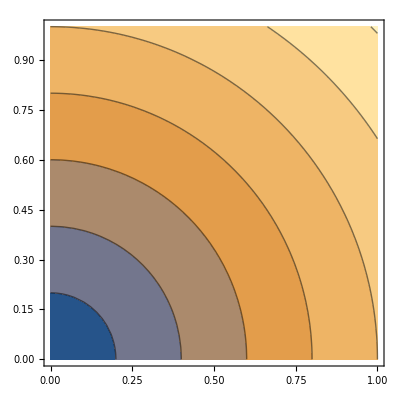

```mathematica
ContourPlot[Sqrt[(x)^2+(y)^2]/.t->0.001,{x,0,1},{y,0,1}]
```

### Pressure:

```mathematica
p[x_,y_,t_]:=x
```

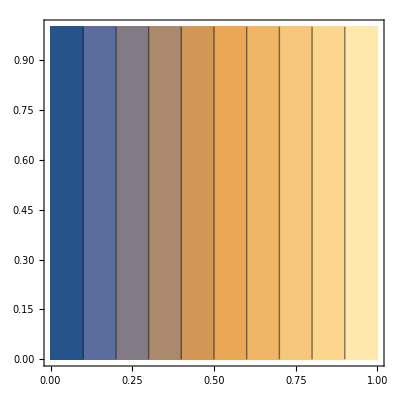

```mathematica
ContourPlot[p[x,y,t],{x,0,1},{y,0,1}]
```

### Elastic Stress:

```mathematica
{D[(x), x],D[(x), y]}//Simplify
```

{1,0}

```mathematica
{D[(y), x],D[(y), y]}//Simplify
```

{0,1}

```mathematica
Gradu[x_,y_,t_]:={{1,0},{0,1}}
```

Let us define ϵ (u) :

```mathematica
w=1/2*(Gradu[x,y,t]+Transpose[Gradu[x,y,t]])//Simplify
```

{{1,0},{0,1}}

Let us compute the stress σ= A^-1 ϵ(u): (Using the expression for A^-1 given in equation (3 . 2 . 9) of Ambartsumyan PhD. Thesis)

```mathematica
σe=2mu w+lambda Tr[w]IdentityMatrix[2]//Simplify
```

{{2 (lambda+mu),0},{0,2 (lambda+mu)}}

Let us define the stress function as the previous expression :

```mathematica
Sigmae[x_,y_,t_]:={{2 (lambda+mu),0},{0,2 (lambda+mu)}}
```

### Stress:

```mathematica
Sigmae[x,y,t]-alpha {{p[x,y,t],0},{0,p[x,y,t]}}//Simplify
```

{{2 (lambda+mu)-alpha x,0},{0,2 (lambda+mu)-alpha x}}

```mathematica
Sigma[x_,y_,t_]:={{2 (lambda+mu)-alpha x,0},{0,2 (lambda+mu)-alpha x}}
```

ContourPlot of the Magnitude of the first row of σ :

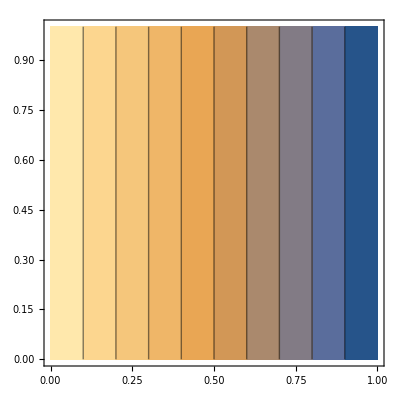

```mathematica
ContourPlot[Sqrt[(2 (lambda+mu)-alpha x)^2+(0)^2]/.{lambda->0,mu->1,alpha->1},{x,0,1},{y,0,1}]
```

ContourPlot of the Magnitude of the second row of σ :

```mathematica
ContourPlot[Sqrt[(0)^2+(2 (lambda+mu)-alpha x)^2]/.{lambda->0,mu->1,alpha->1},{x,0,1},{y,0,1}]
```

-Graphics-

### Rotation :

```mathematica
1/2*(Gradu[x,y,t]-Transpose[Gradu[x,y,t]])//Simplify
```

{{0,0},{0,0}}

ContourPlot of the element in the first row and second column of the rotation:

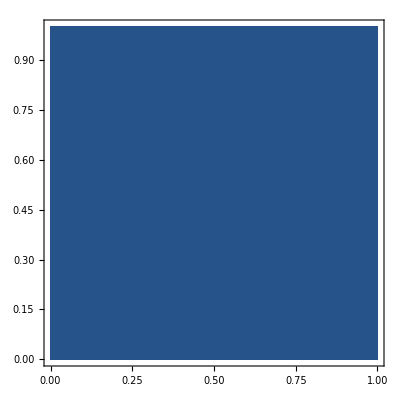

```mathematica
ContourPlot[0,{x,0,1},{y,0,1}]
```

### Darcy velocity :

```mathematica
K = perm*IdentityMatrix[2];
```

```mathematica
-K.{D[p[x,y,t],x],D[p[x,y,t],y]}//Simplify
```

{-perm,0}

```mathematica
z[x_,y_,t_]:={-perm,0}
```

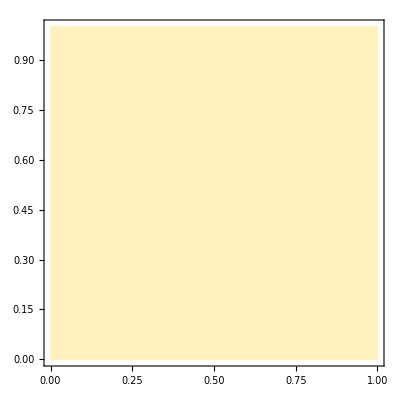

```mathematica
ContourPlot[Sqrt[(-perm )^2+(0)^2]/.perm->1,{x,0,1},{y,0,1}]
```

### Source term f :

```mathematica
Sigma[x,y,t]
```

{{2 (lambda+mu)-alpha x,0},{0,2 (lambda+mu)-alpha x}}

```mathematica
-(D[(2 (lambda+mu)-alpha x),x]+D[0,y])//Simplify
```

alpha

```mathematica
f1[x_,y_,t_]:=alpha
```

```mathematica
-(D[0,x]+D[(2 (lambda+mu)-alpha x),y])//Simplify
```

0

```mathematica
f2[x_,y_,t_]:=0
```

### Source term q :

```mathematica
u[x,y,t]
```

{x,y}

```mathematica
z[x,y,t]
```

{-perm,0}

```mathematica
D[c0 p[x,y,t]+alpha (D[x,x]+D[ y,y]),t]+D[-perm,x]+D[0,y]//Simplify
```

0

```mathematica
q[x_,y_,t_]:=0
```